```mathematica
Tail=Sequence@@#&
```

Sequence@@#1&

```mathematica
cols=Flatten@(Permutations[RGBColor[Tail[#],t]]&/@{{0,0},{0,1},{1,1}})
```

{RGBColor[0,0,t],RGBColor[0,t,0],RGBColor[t,0,0],RGBColor[0,1,t],RGBColor[0,t,1],RGBColor[1,0,t],RGBColor[1,t,0],RGBColor[t,0,1],RGBColor[t,1,0],RGBColor[1,1,t],RGBColor[1,t,1],RGBColor[t,1,1]}

```mathematica
lch[co_LCHColor]:=List@@co
```

```mathematica
luma[LCHColor[l_,c_,h_]]:=l
chroma[LCHColor[l_,c_,h_]]:=c
hue[LCHColor[l_,c_,h_]]:=h
cc[RGBColor[r_Real|r_Integer,g_Real|g_Integer,b_Real|b_Integer],sp_]:=ColorConvert[RGBColor[r,g,b],sp]
cc[LCHColor[r_Real|r_Integer,g_Real|g_Integer,b_Real|b_Integer],sp_]:=ColorConvert[LCHColor[r,g,b],sp]
```

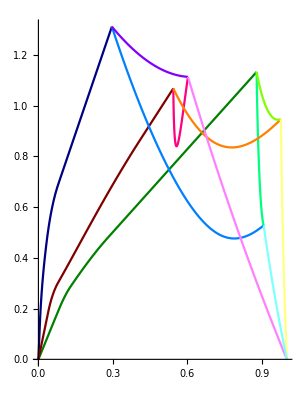

```mathematica
ParametricPlot[Evaluate[{luma@#,chroma@#}&/@(cc[#,LCHColor]&/@cols)],{t,0,1},PlotRange->All,PlotStyle->(cols/.t->.5)]
```

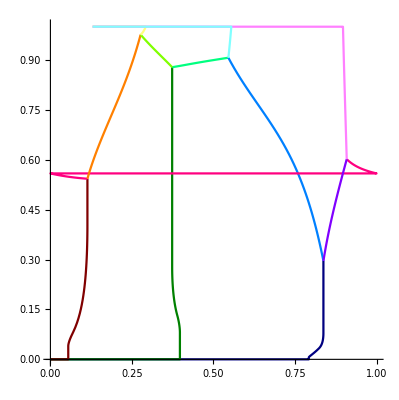

```mathematica
ParametricPlot[Evaluate[{hue@#,luma@#}&/@(cc[#,LCHColor]&/@cols)],{t,0,1},PlotRange->All,PlotStyle->(cols/.t->.5)]
```

```mathematica
?Disk
```

Disk[{x,y},r] represents a disk of radius r centered at {x,y}.
Disk[{x,y}] gives a disk of radius 1. 
Disk[{x,y},{r_x,r_y}] gives an axis-aligned elliptical disk with semiaxes lengths r_x and r_y.
Disk[{x,y},…,{θ_1,θ_2}] gives a sector of a disk from angle θ_1 to θ_2.

```mathematica
Graphics[{EdgeForm[Thick],Pink,Disk[{}]}]
```

RowBox[{"Circle", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], ",", StyleBox["r", "TI"]}], "]"}] represents a circle of radius StyleBox["r", "TI"] centered at RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}].
RowBox[{"Circle", "[", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], "]"}] gives a circle of radius 1. 
RowBox[{"Circle", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["r", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["r", "TI"], StyleBox["y", "TI"]]}], "}"}]}], "]"}] gives an axis-aligned ellipse with semiaxes lengths SubscriptBox[StyleBox["r", "TI"], StyleBox["x", "TI"]] and SubscriptBox[StyleBox["r", "TI"], StyleBox["y", "TI"]].
RowBox[{"Circle", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], ",", StyleBox["…", "TR"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["θ", "TR"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["θ", "TR"], StyleBox["2", "TR"]]}], "}"}]}], "]"}] gives a circular or ellipse arc from angle SubscriptBox[StyleBox["θ", "TR"], StyleBox["1", "TR"]] to SubscriptBox[StyleBox["θ", "TR"], StyleBox["2", "TR"]].

```mathematica
Show[DensityPlot[maxCc3[l,h],{h,0,2},{l,0,1},ColorFunction->GrayLevel,AspectRatio->Automatic,PlotPoints->100],ParametricPlot[Evaluate[{Mod[hue@#+.0001,1],luma@#}&@cc[#,LCHColor]],{t,0,1},PlotRange->All,ColorFunction->Function[{h,l,t},#]]&/@cols,ParametricPlot[Evaluate[{1+Mod[hue@#+.0001,1],luma@#}&@cc[#,LCHColor]],{t,0,1},PlotRange->All,ColorFunction->Function[{h,l,t},#]]&/@cols,Graphics[{RGBColor@@#,EdgeForm[Black],Disk[{hue@#,luma@#}&@cc[RGBColor@@#,LCHColor],.01]}]&/@Tuples[{0,1},3],
Graphics[{RGBColor@@#,EdgeForm[Black],Disk[{1+hue@#,luma@#}&@cc[RGBColor@@#,LCHColor],.01]}]&/@Tuples[{0,1},3]]
```

-Graphics-

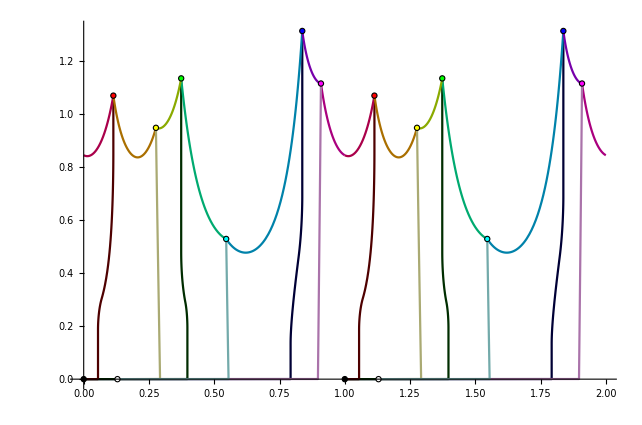

```mathematica
Show[ParametricPlot[Evaluate[{Mod[.0001+hue@#,1],chroma@#}&@cc[#,LCHColor]],{t,0,1},PlotRange->All,ColorFunction->Function[{h,l,t},Darker@#]]&/@cols,ParametricPlot[Evaluate[{1+Mod[.0001+hue@#,1],chroma@#}&@cc[#,LCHColor]],{t,0,1},PlotRange->All,ColorFunction->Function[{h,l,t},Darker@#]]&/@cols,Graphics[{RGBColor@@#,EdgeForm[Black],Disk[{Mod[.0001+hue@#,1],chroma@#}&@cc[RGBColor@@#,LCHColor],.01]}]&/@Tuples[{0,1},3],Graphics[{RGBColor@@#,EdgeForm[Black],Disk[{1+Mod[.0001+hue@#,1],chroma@#}&@cc[RGBColor@@#,LCHColor],.01]}]&/@Tuples[{0,1},3]]
```

```mathematica
Show[ParametricPlot[Evaluate[{Mod[.0001+hue@#,1],chroma@#}&@cc[#,LCHColor]],{t,0,1},PlotRange->All,PlotStyle->(#/.t->.5)]&/@cols,Graphics[{RGBColor@@#,EdgeForm[Black],Disk[{Mod[.0001+hue@#,1],chroma@#}&@cc[RGBColor@@#,LCHColor],.01]}]&/@Tuples[{0,1},3],PlotRange->All]
```

```mathematica
lch[cc[RGBColor[0,0,0],LCHColor]]
```

{0.,0.,0.}

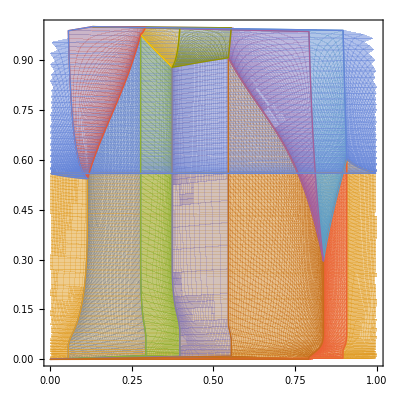

```mathematica
ParametricPlot[Evaluate[Tail[({hue@#,luma@#}&/@(cc[#,LCHColor]&/@Permutations[RGBColor[r,g,#]]))]&/@{0,1}],{r,0,1},{g,0,r}]
```

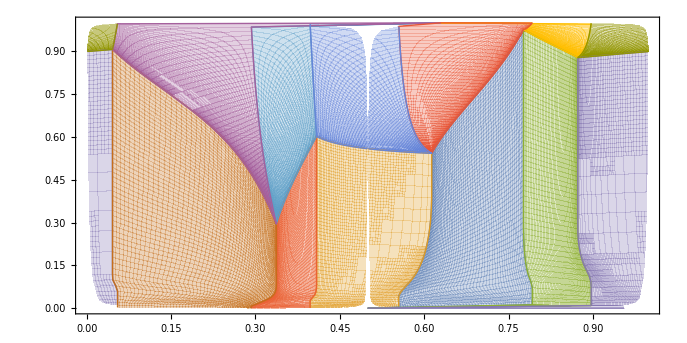

```mathematica
ParametricPlot[Evaluate[Tail[({Mod[(hue@#)+.5,1],luma@#}&/@(cc[#,LCHColor]&/@Permutations[RGBColor[r,g,#]]))]&/@{0,1}],{r,0,1},{g,0,r},AspectRatio->1/2]
```

```mathematica
?Inter
```

```mathematica
Flatten@(Permutations[RGBColor[r,r,#]]&/@{0,1})/.RGBColor[
```

{RGBColor[r,r,0],RGBColor[r,0,r],RGBColor[0,r,r],RGBColor[r,r,1],RGBColor[r,1,r],RGBColor[1,r,r]}

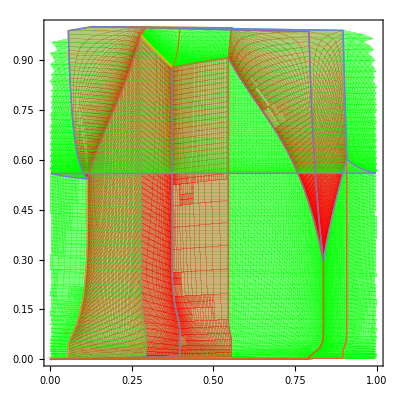

```mathematica
ParametricPlot[Evaluate[Tail[({hue@#,luma@#}&/@(cc[#,LCHColor]&/@{RGBColor[r,g,#1],RGBColor[r,#1,g],RGBColor[#1,r,g]}))]&/@{0,1}],{r,0,1},{g,0,1},PlotStyle->{Red,Green}]
```

```mathematica
maxC[l_,h_]:=FixedPoint[ColorConvert[ColorConvert[LCHColor[l,#,h],RGBColor],LCHColor][[2]]&,2]
```

```mathematica
maxCc=Compile[{{l,_Real},{h,_Real}},FixedPoint[chroma[ColorConvert[ColorConvert[LCHColor[l,#,h],RGBColor],LCHColor]]&,2]]
```

CompiledFunction[…]

```mathematica
maxCc2=Compile[{{l,_Real},{h,_Real}},FixedPoint[chroma[ColorConvert[ColorConvert[LCHColor[l,#,h],RGBColor],LCHColor]]&,2,50]]
```

CompiledFunction[…]

```mathematica
maxCc3=Compile[{{l,_Real},{h,_Real}},FixedPoint[chroma[ColorConvert[ColorConvert[LCHColor[l,#,h],RGBColor],LCHColor]]&,2,50,SameTest->(Abs[#1-#2]<.01&)]]
```

CompiledFunction[…]

```mathematica
GrayLevel/@Range[.2,.8,.06]
```

{GrayLevel[0.2],GrayLevel[0.26],GrayLevel[0.32],GrayLevel[0.38],GrayLevel[0.44],GrayLevel[0.5],GrayLevel[0.56],GrayLevel[0.62],GrayLevel[0.6799999999999999],GrayLevel[0.74],GrayLevel[0.8]}

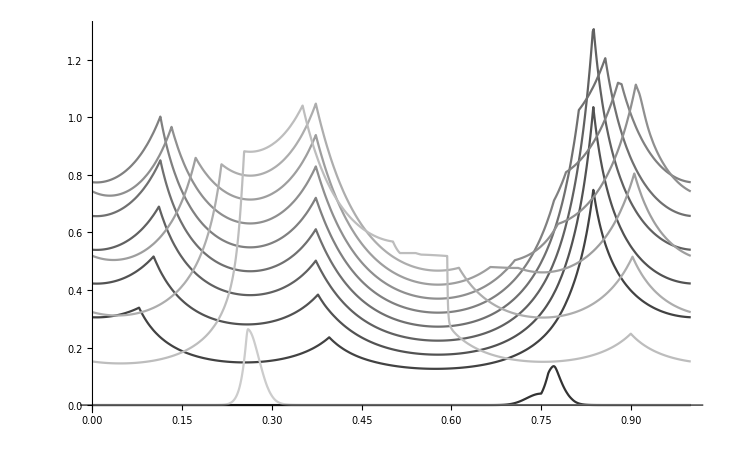

```mathematica
Plot[Evaluate[maxCc2[#,h]&/@Range[0,1,.1]],{h,0,1},PlotStyle->{GrayLevel[0.2],GrayLevel[0.26],GrayLevel[0.32],GrayLevel[0.38],GrayLevel[0.44],GrayLevel[0.5],GrayLevel[0.56],GrayLevel[0.62],GrayLevel[0.6799999999999999],GrayLevel[0.74],GrayLevel[0.8]}]
```

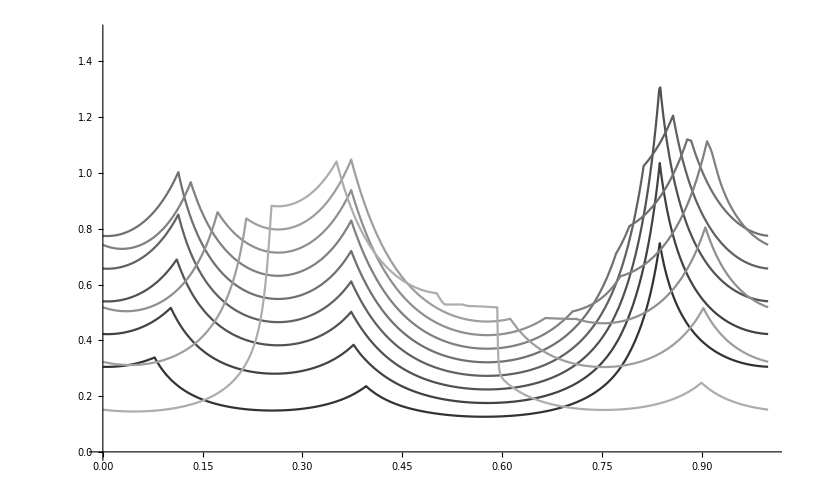

```mathematica
Plot[Evaluate[maxCc3[#,h]&/@Range[.1,.9,.1]],{h,0,1},PlotStyle->{GrayLevel[0.2],GrayLevel[0.26],GrayLevel[0.32],GrayLevel[0.38],GrayLevel[0.44],GrayLevel[0.5],GrayLevel[0.56],GrayLevel[0.62],GrayLevel[0.6799999999999999],GrayLevel[0.74],GrayLevel[0.8]},PlotRange->{0,1.5}]
```

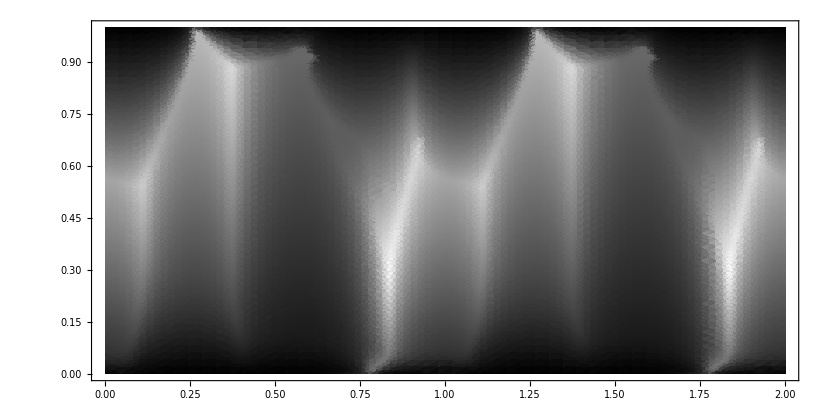

```mathematica
DensityPlot[maxCc3[l,h],{h,0,2},{l,0,1},AspectRatio->Automatic,ColorFunction->GrayLevel,PlotPoints->50]
```

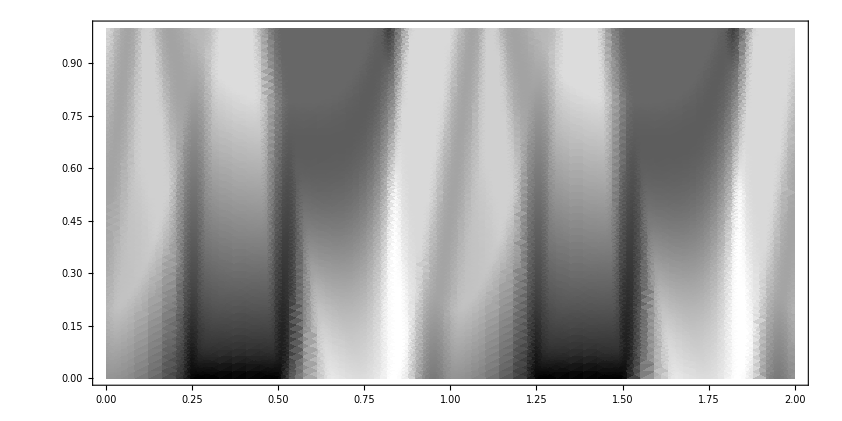

```mathematica
DensityPlot[iter[l,2,h],{h,0,2},{l,0,1},AspectRatio->Automatic,ColorFunction->GrayLevel,PlotPoints->50]
```

```mathematica
luma[ColorConvert[RGBColor[1,1,0],LCHColor]]
```

0.976071

```mathematica
Table[Print[maxC[.5,h]],{h,0,1,.1}];//Timing
```

0.774693

0.939208

0.597896

$Aborted

```mathematica
maxCc[.5,.3]
```

$Aborted

```mathematica
LCHColor[.5,2,.3]
```

LCHColor[0.5, 2, 0.3]

```mathematica
?Hue
```

Hue[h] is a graphics directive which specifies that objects which follow are to be displayed, in a color corresponding to hue h. 
Hue[h,s,b] specifies colors in terms of hue, saturation, and brightness. 
Hue[h,s,b,a] specifies opacity a.

```mathematica
FixedPoint[ColorConvert[ColorConvert[LCHColor[.5,#,.4],RGBColor],LCHColor][[2]]&,2]
```

0.582413

```mathematica
Hue[.5]
```

Hue[0.5]

```mathematica
iter[l_,c_,h_]:=chroma[ColorConvert[ColorConvert[LCHColor[l,c,h],RGBColor],LCHColor]]
```

```mathematica
FixedPoint[chroma[ColorConvert[ColorConvert[LCHColor[.5,#,.3],RGBColor],LCHColor]]&,2]
```

$Aborted

```mathematica
?NestList
```

NestList[f,expr,n] gives a list of the results of applying f to expr 0 through n times.

```mathematica
Evaluate[lch[cc[cc[LCHColor[1,c,0],RGBColor],LCHColor]]]/.c->2
```

lch[cc[cc[LCHColor[1, 2, 0],RGBColor],LCHColor]]

```mathematica
?ColorDistance
```

ColorDistance[c_1,c_2] gives the approximate perceptual distance between color directives c_1 and c_2.
ColorDistance[list,c] gives color distances between elements of list and c.
ColorDistance[list_1,list_2] gives color distances between corresponding elements of list_1 and list_2.
ColorDistance[image,c] gives an image whose pixel values are color distance between pixels in image and the color c.
ColorDistance[image_1,image_2] yields an image giving the pixelwise color distance between image_1 and image_2.

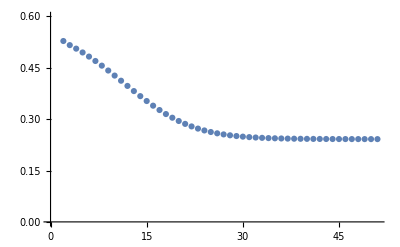

```mathematica
ListPlot[NestList[chroma[ColorConvert[ColorConvert[LCHColor[.9,#,.61],RGBColor],LCHColor]]&,2,50],PlotRange->{0,.6}]
```

```mathematica
?Nest
```

Nest[f,expr,n] gives an expression with f applied n times to expr.

```mathematica
?FixedPoint
```

FixedPoint[f,expr] starts with expr, then applies f repeatedly until the result no longer changes.

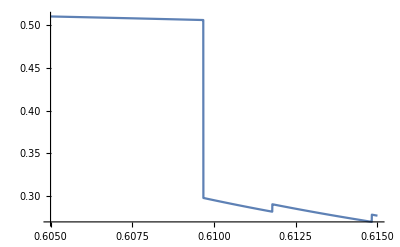

```mathematica
Plot[maxCc3[.9,x],{x,.605,.615}]
```

```mathematica
LCHColor[.9,.3,.61]
LCHColor[.9,.5,.61]
```

LCHColor[0.9, 0.3, 0.61]

LCHColor[0.9, 0.5, 0.61]

```mathematica
List@@cc[cc[RGBColor[0,1,1],LCHColor],RGBColor]
```

{0.,1.,0.999999}

```mathematica
lch@cc[RGBColor[.8,.8,1],LCHColor]
```

{0.833287,0.262965,0.797692}

```mathematica
List@@cc[cc[LCHColor[.8,10^-4.,.8],RGBColor],LCHColor]
```

{0.8,0.0000995738,0.800946}

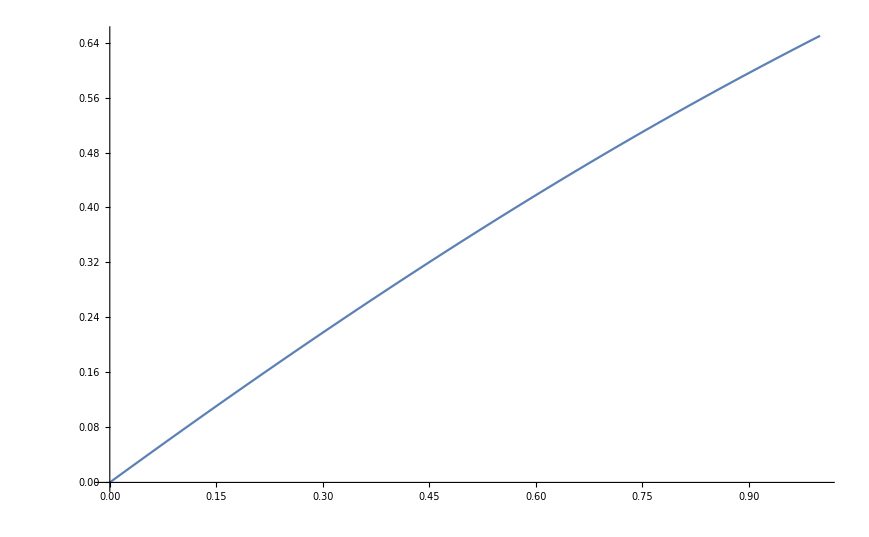

```mathematica
Plot[ColorDistance[LCHColor[1,c,0],cc[cc[LCHColor[1,c,0],RGBColor],LCHColor]],{c,10^-8,1}]
```

```mathematica
cd[a_LCHColor,b_LCHColor]:=ColorDistance[a,b,DistanceFunction->"CIE94"]
```

```mathematica
cdlch=Compile[{{l,_Real},{c,_Real},{h,_Real}},ColorDistance[LCHColor[l,c,h],ColorConvert[ColorConvert[LCHColor[l,c,h],RGBColor],LCHColor],DistanceFunction->"CIE94"]]
```

```mathematica
cdlch0=Compile[{{l,_Real},{c,_Real},{h,_Real}},ColorDistance[LCHColor[l,c,h],ColorConvert[ColorConvert[LCHColor[l,c,h],RGBColor],LCHColor],DistanceFunction->"CIE2000"]]
```

CompiledFunction[…]

```mathematica
cd[LCHColor[l,c,h],cc[cc[LCHColor[l,c,h],RGBColor],LCHColor]]/.{l->.95,c->.1,h->.05}
```

0.0232697

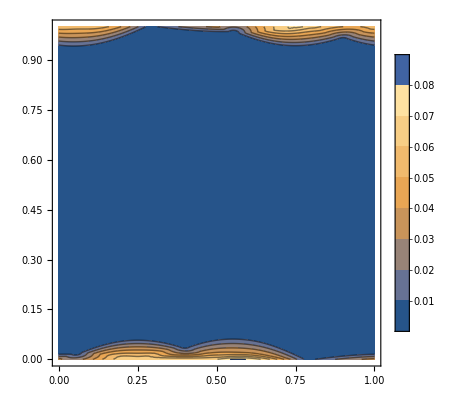
{2.2485,-Graphics-}

```mathematica
With[{c=.1},
ContourPlot[cd[LCHColor[l,c,h],cc[cc[LCHColor[l,c,h],RGBColor],LCHColor]],{h,0,1},{l,0,1},PlotLegends->Automatic,PlotPoints->50,PlotRange->{0,.1}]]//Timing
```

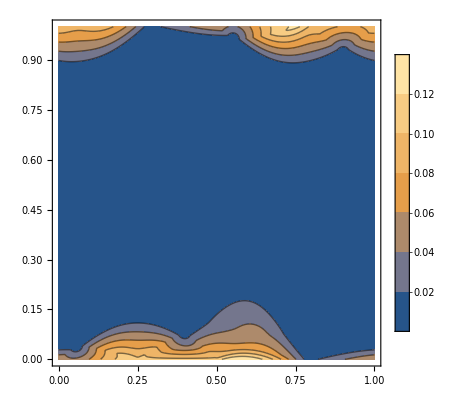

```mathematica
With[{c=.2},
ContourPlot[cdlch[l,c,h],{h,0,1},{l,0,1},PlotLegends->Automatic,PlotPoints->50,PlotRange->{0,.2}]]
```

```mathematica
?MaxValue
```

MaxValue[f,x] gives the maximum value of f with respect to x.
MaxValue[f,{x,y,…}] gives the maximum value of f with respect to x, y, …. 
MaxValue[{f,cons},{x,y,…}] gives the maximum value of f subject to the constraints cons. 
MaxValue[…,x∈reg] constrains x to be in the region reg.
MaxValue[…,…,dom] constrains variables to the domain dom, typically Reals or Integers.

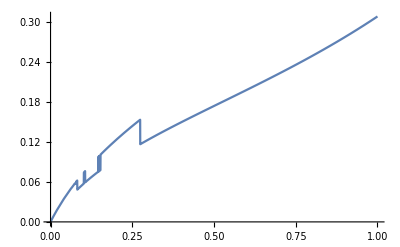

```mathematica
Plot[With[{c=ccc},
MaxValue[{cd[LCHColor[l,c,h],cc[cc[LCHColor[l,c,h],RGBColor],LCHColor]],0<l<1,0<h<1},{l,h}]],{ccc,0,1}]
```

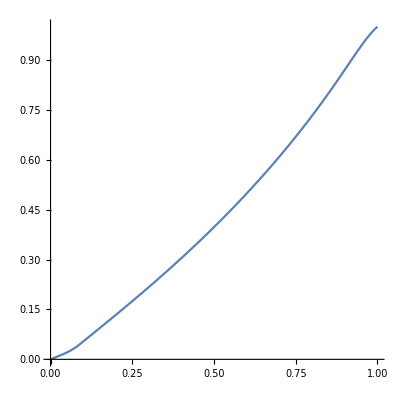

```mathematica
Plot[ColorDistance[GrayLevel[0.],GrayLevel[x],DistanceFunction->"CIE2000"],{x,0,1},AspectRatio->1]
```

```mathematica
Maximize[{c,cd[LCHColor[l,c,h],cc[cc[LCHColor[l,c,h],RGBColor],LCHColor]]<.1},c]/.{h->.5,l->.5}
```

{0.469288,{c→0.469288}}

```mathematica
tab=Table[Timing[Maximize[{c,cdlch[l,c,h]<.01},c][[1]]],{h,0,1,.1},{l,0,1,.1}];
```

```mathematica
tab[[All,All,1]]//MatrixForm
```

(1.45326 | 1.01949 | 1.20542 | 1.14358 | 0.83456 | 1.01409 | 0.927146 | 0.797523 | 1.1244 | 1.1716 | 1.21545
1.33367 | 1.57154 | 0.902156 | 1.02251 | 1.15732 | 1.02596 | 0.766882 | 1.1173 | 1.20511 | 1.16573 | 1.07611
1.12247 | 1.05313 | 0.766889 | 0.999176 | 0.778534 | 1.49197 | 0.962709 | 0.956877 | 1.03437 | 0.942348 | 1.04545
0.774257 | 0.810082 | 1.00645 | 1.76394 | 1.32754 | 1.33771 | 1.02368 | 1.36318 | 1.03979 | 1.88865 | 1.26024
1.1016 | 1.26849 | 1.24115 | 2.07894 | 0.95117 | 2.04512 | 1.77552 | 1.4193 | 1.20806 | 1.3528 | 1.43
1.31749 | 1.57523 | 1.12101 | 1.56951 | 1.7955 | 1.06051 | 1.59894 | 0.775334 | 1.60037 | 1.56281 | 1.03418
0.989061 | 1.18456 | 0.921916 | 0.8648 | 0.944381 | 1.45489 | 1.07652 | 1.71354 | 1.08241 | 0.794043 | 1.57525
1.28955 | 1.1817 | 0.993299 | 1.10372 | 1.7051 | 1.16673 | 1.03974 | 1.08575 | 0.861338 | 1.76565 | 1.19458
1.41392 | 0.923887 | 0.951021 | 1.21722 | 1.07471 | 1.01153 | 1.11677 | 1.03839 | 1.06634 | 1.23374 | 1.1711
1.20783 | 1.03641 | 1.04015 | 1.03056 | 1.05875 | 1.75952 | 1.38945 | 0.853928 | 0.837159 | 1.25282 | 1.29998
1.07236 | 1.00369 | 1.04085 | 0.872458 | 0.760078 | 0.805864 | 0.902811 | 0.77132 | 1.1047 | 1.05705 | 1.1119)

```mathematica
tab[[All,All,2]]//MatrixForm
```

(0.0261333 | 0.327018 | 0.446833 | 0.566214 | 0.685254 | 0.804021 | 0.775102 | 0.551139 | 0.351644 | 0.173449 | 0.0139487
0.0219848 | 0.294036 | 0.544298 | 0.68602 | 0.830785 | 0.974712 | 0.872025 | 0.599843 | 0.37012 | 0.177061 | 0.0138626
0.0117657 | 0.174999 | 0.324558 | 0.444871 | 0.539957 | 0.483068 | 0.728083 | 0.822096 | 0.722144 | 0.305565 | 0.0221284
0.0104712 | 0.173493 | 0.315218 | 4.21795 | 0.510321 | 0.599366 | 0.688386 | 0.777386 | 0.866369 | 3.08037 | 0.136755
0.0104712 | 0.258618 | 0.346512 | 1.99475 | 0.528817 | 1.72381 | 0.155116 | 0.801642 | 0.892448 | 0.847827 | 0.0367831
0.0104713 | 0.783 | 0.215724 | 0.22785 | 0.231413 | 0.384791 | 4.20025 | 0.497099 | 6.6694 | 2.00078 | 0.0263368
0.0107977 | 0.143578 | 0.194361 | 0.245177 | 0.295923 | 2.23221 | 0.397226 | 1.16104 | 0.498302 | 0.288637 | 0.031948
0.0191381 | 0.184971 | 0.250809 | 0.316578 | 1.21084 | 0.447959 | 0.513586 | 0.508823 | 0.34162 | 2.49636×10^104 | 0.0127628
0.142127 | 0.435105 | 0.590811 | 0.746089 | 0.900967 | 0.863323 | 0.690846 | 0.517519 | 0.345482 | 0.176453 | 0.0113142
0.0363834 | 0.432115 | 0.589086 | 0.744997 | 0.900165 | 3.69017 | 1.10092 | 0.820948 | 0.553894 | 0.279401 | 0.014756
0.0261333 | 0.327018 | 0.446833 | 0.566214 | 0.685254 | 0.80402 | 0.775102 | 0.551139 | 0.351644 | 0.173449 | 0.0139487)

```mathematica
tab0=Table[Timing[Maximize[{c,cdlch0[l,c,h]<.01},c][[1]]],{h,0,1,.1},{l,0,1,.1}];
```

```mathematica
(tab0-tab)[[All,All,2]]//MatrixForm
```

(-0.00465067 | 0.00285274 | 0.00367909 | 0.0037112 | 1.05023 | 0.000909218 | 0.472024 | 0.0052052 | 0.00316353 | -0.00159401 | -0.00428926
-0.002302 | -0.00194699 | 0.00337062 | -0.0000933405 | -0.00101212 | -0.00266408 | 0.00466762 | 0.644593 | 0.00236066 | -0.00327305 | -0.00430544
-0.000264082 | -0.0021909 | -0.00184348 | -0.00237709 | -0.00304767 | 0.147157 | -0.00462138 | -0.00546477 | -0.00826756 | -0.00504011 | -0.006974
-0.000801655 | -0.00064502 | -0.000615235 | -3.91369 | -0.00097266 | -0.00114987 | -0.00132598 | -0.00150889 | -0.00169668 | -2.12692 | -0.0276625
-0.00288412 | -0.000973442 | 0.0025056 | -1.63287 | -0.12378 | -1.0993 | 0.561612 | -0.780479 | 0.00872324 | 0.0529857 | -0.0071541
-0.00365109 | -0.651074 | -0.0601408 | 0.0432776 | 0.0965731 | -0.000603003 | -4.10473 | 0.000399315 | -6.11531 | -1.39165 | -0.00473335
-0.00361643 | -0.003208 | -0.00248978 | -0.00132721 | -0.000336008 | 0.668042 | 0.000695073 | -0.71193 | 0.0019205 | 0.00213855 | 0.00251613
-0.00643054 | -0.00361844 | -0.00251801 | -0.0016326 | -0.829832 | -0.00120432 | -0.000681167 | 0.0075462 | 0.00608522 | -2.49636×10^104 | -0.000220104
0.809936 | -0.00958147 | -0.0118173 | -0.0139749 | -0.016121 | 0.0151655 | 0.0174135 | 1.04872 | 0.630219 | 0.885537 | -0.000692008
-0.00710424 | 0.00542022 | 0.00670773 | 0.00620401 | 0.00360858 | -2.63536 | 0.00370087 | 0.00255268 | 0.00287173 | 0.000260183 | -0.00394809
-0.00465067 | 0.00285266 | 0.003679 | 0.00371112 | 1.05023 | 0.000910679 | 0.00430883 | 0.0052052 | 0.00316353 | -0.00159401 | -0.00428926)

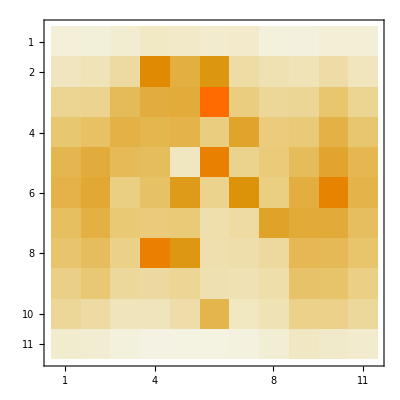

```mathematica
tab[[All,All,2]]/.{2.496362167490794*^104->.2}//Transpose//Reverse//MatrixPlot
```

```mathematica
cdlch[.8,2,.5]
```

0.177217

```mathematica
(Maximize[{c,cdlch[l,c,h]<.01},c])/.{h->.5,l->.8}
```

{6.6694,{c→6.6694}}

```mathematica
img=ColorConvert[-Graphics-,"LCH"];
```

```mathematica
MapThread[Labeled,
{{ImageApply[({L,C,h}↦{.5+(L-.5),2C,h})@@#&,img]},
Text/@{birb}}
]
```

{-Graphics-birb}